```mathematica
SetDirectory[NotebookDirectory[]];
```

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ=75.8;
ν=-482.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=300;
```

# Mean-field effective potential

## effective potential

92.325526

135.695

480.438

300.058

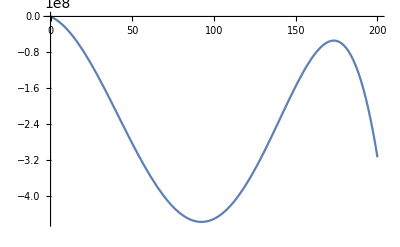

```mathematica
a=FindMinimum[{V[a1^2/2,h,1,0.,λ,ν,c]+Vvacuum[a1^2/2,h,M1],0<a1<195},{a1,90},WorkingPrecision->8][[2]][[1]][[2]]//Quiet

√Vd1rhovacuum[a^2/2,h,λ,ν,M1]
√(Vd1rhovacuum[a^2/2,h,λ,ν,M1]+2*a^2/2*Vd2rhovacuum[a^2/2,h,λ,ν,M1])
√mf2[h,a^2/2]
Plot[{V[a^2/2,h,1,0,λ,ν,c]+Vvacuum[a^2/2,h,M1]},{a,0,200},PlotRange->All]
(*Zps[a^2/2,h,1.,0.,400]*)
```

```mathematica
(*fpi=Flatten[Table[{FindMinimum[{V[a^2/2,h,i,μ,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]];*)
```

```mathematica
ListPlot[fpi,PlotRange->All]
```

ListPlot::lpn: fpi 不是由数字或者数对组成的列表.

ListPlot[fpi,PlotRange→All]

# Mean-field wave function renormalization

## threshold functions and equations

```mathematica
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,500.,10000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
```

## Zps(0)

## Z_π data

```mathematica
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
```

```mathematica
Zall=Flatten[Table[Zps[(sigmadata[[1]][[i]])^2/2,h,N[i],0.,300.],{i,1,300,1}]];
```

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

General::stop: 在本次计算中，NIntegrate::izero 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {q} = {197.75} 处的 q 中进行 10 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 3.72751×10^-25 和 1.03042×10^-30.

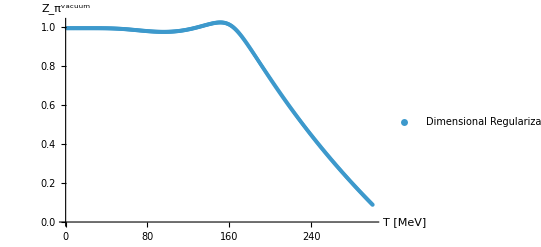

```mathematica
plotvac=ListPlot[{Zall},PlotRange->All,AxesLabel->{"T [MeV]","Z_π^vacuum"},PlotLegends->{"Dimensional Regularization  M=500 MeV","UV cut-off   Λ=700 MeV"}]
```

```mathematica
Export["./vac.pdf",plotvac]
```

./vac.pdf

# Mean-field two-point function

## threshold functions

```mathematica
F1[q_,ρ_,h_,T_,μ_]:=q/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^3/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((-0.+nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
```

## thermal equation

```mathematica
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^3 NIntegrate[q^2/q(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)/q^2 F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,500.,5000.},{x,-1,1},{y,0,2π},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
```

## Regularized vacuum

```mathematica
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]-(Nc h^2 mf2[h,ρ])/(16 π^2)(*+(p0^2+ps^2)/2NIntegrate[Log[(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])/MZ^2],{x,0,1}]*));
```

## full two-point function

```mathematica
gamma2[p0_,ps_,ρ_,h_,T_,μ_,Mmass_,MZ_]:=(*gamma2thr[p0,ps,ρ,h,T,μ]+*)gammavac[p0,ps,ρ,h,Mmass,MZ];
```

```mathematica
gammadata=Flatten[ParallelTable[gamma2[-ⅈ(i*10+ⅈ 0.5),0.,(fpi300[[6]][[100]])^2/2,h,100.,0.,300.,300.]+(-ⅈ(i*10))^2+(0.)^2+(λ (fpi300[[6]][[100]])^2/2+ν),{i,1,100}]];
```

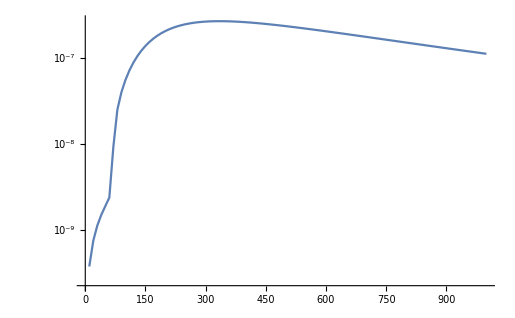

```mathematica
ListLinePlot[Transpose[{Flatten[Table[i*10,{i,1,100}]],-1/π Im[gammadata]/(Re[gammadata]^2+Im[gammadata]^2)}],PlotRange->All,ScalingFunctions->"Log"]
```

# Mean-field spec

## threshold functions

```mathematica
F1[q_,ρ_,h_,T_,μ_]:=q/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1mp1[q_,omega_,ϵ_,ps_,x_,ρ_,h_,T_,μ_]:=q^3/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((-0.+nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ (-ⅈ(omega+ⅈ ϵ))-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ (-ⅈ(omega+ⅈ ϵ))+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
F1F1mp2[q_,omega_,ϵ_,ps_,x_,ρ_,h_,T_,μ_]:=If[omega<ps,q^3/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ (-ⅈ(omega+ⅈ ϵ))-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ (-ⅈ(omega+ⅈ ϵ))+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))),0.];
```

## thermal equation

```mathematica
gamthr[omega_,ϵ_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^3 NIntegrate[q^2/q((*2F1[q,ρ,h,T,μ]*)-((-ⅈ(omega+ⅈ ϵ))^2+ps^2)/q^2(F1F1mp1[q,omega,ϵ,ps,x,ρ,h,T,μ]+F1F1mp2[q,omega,ϵ,ps,x,ρ,h,T,μ])),{q,0.,500.,5000.},{x,-1,1},{y,0,2π},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
```

## Regularized vacuum

```mathematica
gamvac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]-(Nc h^2 mf2[h,ρ])/(16 π^2)+(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1}]);
```

## full two-point function

```mathematica
gam[omega_,ϵ_,ps_,ρ_,h_,T_,μ_,Mmass_,MZ_]:=gamthr[omega,ϵ,ps,ρ,h,T,μ](*+gammavac[p0,ps,ρ,h,Mmass,MZ]*);
```

```mathematica
gammadata=Flatten[ParallelTable[gamma2[-ⅈ(i*10+ⅈ 0.5),0.,(fpi300[[6]][[100]])^2/2,h,100.,0.,300.,300.]+(-ⅈ(i*10))^2+(0.)^2+(λ (fpi300[[6]][[100]])^2/2+ν),{i,1,100}]];
```

```mathematica
ListLinePlot[Transpose[{Flatten[Table[i*10,{i,1,100}]],-1/π Im[gammadata]/(Re[gammadata]^2+Im[gammadata]^2)}],PlotRange->All,ScalingFunctions->"Log"]
```

-Graphics-

# Plot data

## fpi

```mathematica
fpiT50mu=Table[Flatten[ParallelTable[{FindMinimum[{V[a^2/2,h,i,j*4.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]//Quiet},{i,10,10}]],{j,1,100,1}];
```

```mathematica
muT1=Table[i*4,{i,1,100,1}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172,176,180,184,188,192,196,200,204,208,212,216,220,224,228,232,236,240,244,248,252,256,260,264,268,272,276,280,284,288,292,296,300,304,308,312,316,320,324,328,332,336,340,344,348,352,356,360,364,368,372,376,380,384,388,392,396,400}

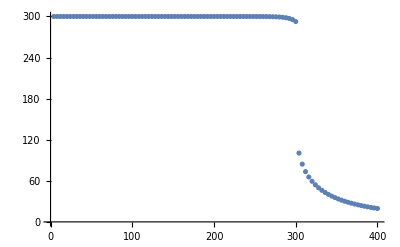

```mathematica
ListPlot[Transpose[{muT1,Flatten[fpiT50mu]*6.5/2}]]
```

```mathematica
Export["./sigmaT50_mu.dat",fpiT50mu];
Export["./mu5to500.dat",muT1];
```

```mathematica
fpimu0=Table[Flatten[ParallelTable[{FindMinimum[{V[a^2/2,h,i,j*5.,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->5,PrecisionGoal->5][[2]][[1]][[2]]//Quiet},{i,1,1500}]],{j,0,0}];
```

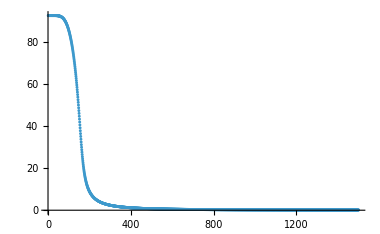

```mathematica
ListPlot[fpimu0,PlotRange->All]
```

```mathematica
sigma1=Import["./sigma0.dat"];
mu=Table[i*5,{i,1,80}]
Export["./sigmaT1.dat",Transpose[sigma1][[1]]]
Export["./mu.dat",mu]
```

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400}

./sigmaT1.dat

./mu.dat

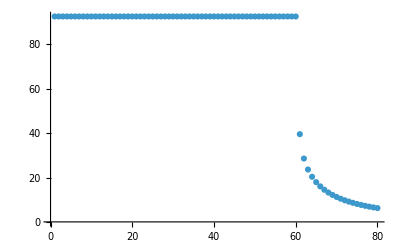

```mathematica
ListPlot[Transpose[sigma1][[1]]]
```

```mathematica
Export["sigma0.dat",fpimu0]
```

sigma0.dat

```mathematica
fpip2=Table[Flatten[ParallelTable[{FindMinimum[{V[a^2/2,h,i,j,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]},{i,1,300}]],{j,290,310,1}]//Quiet;
```

```mathematica
Export["sigma0p2.dat",fpip2]
```

sigma0p2.dat

```mathematica
fpiT1mu=ParallelTable[Flatten[Table[{FindMinimum[{V[a^2/2,h,i,300+j,λ,ν,c]+Vvacuum[a^2/2,h,M1],0<a<95},{a,50},AccuracyGoal->10,PrecisionGoal->10][[2]][[1]][[2]]//Quiet},{i,1,1}]],{j,1,150,1}];
```

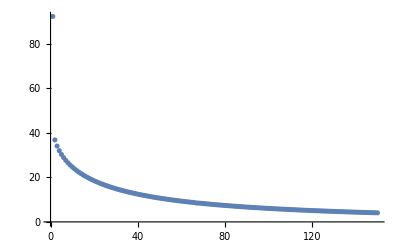

```mathematica
ListPlot[Transpose[fpiT1mu],PlotRange->All]
```

```mathematica
Export["fpiT1.dat",fpiT1mu]
```

fpiT1.dat

## Z_π(p=0)

### M=700

```mathematica
Zmu0=Flatten[Table[Zps[fpimub0[[i]]^2/2,h(*indata[[i]]*),N[i],0.,700.],{i,1,300}]];
```

```mathematica
Zmu200=Flatten[Table[Zps[fpimu200[[i]]^2/2,h(*indata[[i]]*),N[i],200.,700.],{i,1,300}]];
```

```mathematica
Zmu250=Flatten[Table[Zps[fpimu250[[i]]^2/2,h(*indata[[i]]*),N[i],250.,700.],{i,1,300}]];
```

```mathematica
Zmu295=Flatten[Table[Zps[fpimu295[[i]]^2/2,h(*indata[[i]]*),N[i],295.,700.],{i,1,300}]];
```

```mathematica
Zmu300=Flatten[Table[Zps[fpimu300[[i]]^2/2,h(*indata[[i]]*),N[i],300.,700.],{i,1,300}]];
```

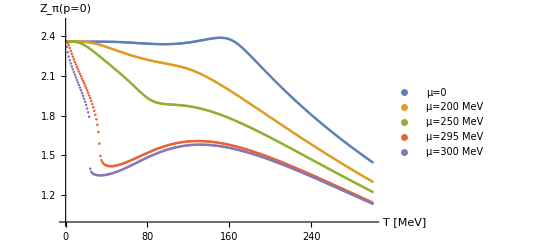

```mathematica
Zplot=ListPlot[{Zmu0,Zmu200,Zmu250,Zmu295,Zmu300},AxesLabel->{"T [MeV]","Z_π(p=0)"},PlotRange->{All,{1,2.5}},PlotLegends->{"μ=0","μ=200 MeV","μ=250 MeV","μ=295 MeV","μ=300 MeV"}]
```

```mathematica
Export["ZM700.pdf",Zplot]
```

ZM700.pdf

### M=300

```mathematica
Zmu0M300=Flatten[ParallelTable[Zps[(fpimu0[[1]][[i]])^2/2,h,N[i],0.,300.]//Quiet,{i,1,1500}]];
```

```mathematica
Zmu200M300=Flatten[Table[Zps[fpimu200[[i]]^2/2,h(*indata[[i]]*),N[i],200.,300.],{i,1,300}]];
```

```mathematica
Zmu250M300=Flatten[Table[Zps[fpimu250[[i]]^2/2,h(*indata[[i]]*),N[i],250.,300.],{i,1,300}]];
```

```mathematica
Zmu295M300=Flatten[Table[Zps[fpimu295[[i]]^2/2,h(*indata[[i]]*),N[i],295.,300.],{i,1,300}]];
```

```mathematica
Zmu300M300=Flatten[Table[Zps[fpimu300[[i]]^2/2,h(*indata[[i]]*),N[i],300.,300.],{i,1,300}]];
```

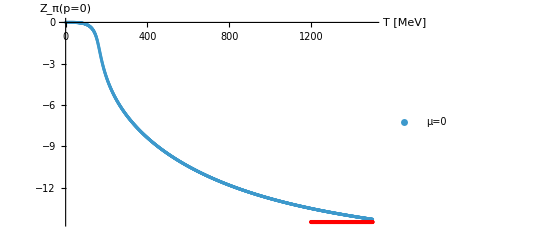

```mathematica
Λ=1500.;
l=Length[fpimu0[[1]]];
ZplotM300=Show[ListPlot[{Zmu0M300(*,Zmu200M300,Zmu250M300,Zmu295M300,Zmu300M300*)},AxesLabel->{"T [MeV]","Z_π(p=0)"},PlotRange->{All,All},PlotLegends->{"μ=0","μ=200 MeV","μ=250 MeV","μ=295 MeV","μ=300 MeV"}],ListPlot[Table[{i,(*Zpsvac[(fpimu0[[1]][[l]])^2/2,h,300.]+1.*)-(h^2 Nc)/(12 π^2)-(h^2 Nc)/(24 π^2)(-(2 Λ^3+3mf2[h,(fpimu0[[1]][[l]])^2/2]Λ)/((mf2[h,(fpimu0[[1]][[l]])^2/2]+Λ^2)^(3/2))+3/2 Log[mf2[h,(fpimu0[[1]][[l]])^2/2]]-3Log[-Λ+√(mf2[h,(fpimu0[[1]][[l]])^2/2]+Λ^2)])},{i,1200,1500}],PlotStyle->Red],PlotRange->{{0,1500},All}]
```

```mathematica
(*Export["ZM300.pdf",ZplotM300]*)
```

### M=300 h(T)

```mathematica
Zmu0M300=Flatten[Table[Zps[fpimub0[[i]]^2/2,hindata[[i]],N[i],0.,300.],{i,1,250}]];
```

```mathematica
Zmu200M300=Flatten[Table[Zps[fpimu200[[i]]^2/2,hindata[[i]],N[i],200.,300.],{i,1,250}]];
```

```mathematica
Zmu250M300=Flatten[Table[Zps[fpimu250[[i]]^2/2,hindata[[i]],N[i],250.,300.],{i,1,250}]];
```

```mathematica
Zmu295M300=Flatten[Table[Zps[fpimu295[[i]]^2/2,hindata[[i]],N[i],295.,300.],{i,1,250}]];
```

```mathematica
Zmu300M300=Flatten[Table[Zps[fpimu300[[i]]^2/2,hindata[[i]],N[i],300.,300.],{i,1,250}]];
```

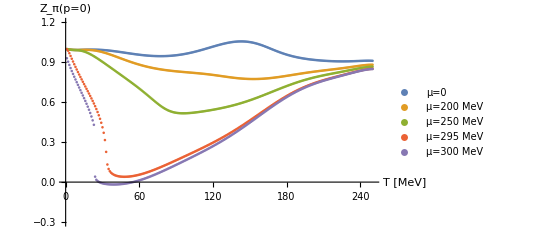

```mathematica
ZplotM300hT=ListPlot[{Zmu0M300,Zmu200M300,Zmu250M300,Zmu295M300,Zmu300M300},AxesLabel->{"T [MeV]","Z_π(p=0)"},PlotRange->{All,{-0.3,1.2}},PlotLegends->{"μ=0","μ=200 MeV","μ=250 MeV","μ=295 MeV","μ=300 MeV"}]
```

```mathematica
Export["ZM300hT.pdf",ZplotM300hT]
```

ZM300hT.pdf